## Grid count

```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2025-03-20-15-56-53.json"];
raw=Association[#]&/@raw;

raw[[1]]
```

<|L0APhaseOffset→0.,solSet→-0.41,impactGridCount→5.,norm_emit_x→8.1512×10^-6,norm_emit_y→8.1396×10^-6,norm_emit_x_90→5.4351×10^-6,norm_emit_y_90→5.3917×10^-6,emitSI90_x→7.8667×10^-6,emitSI90_y→9.8081×10^-6|>

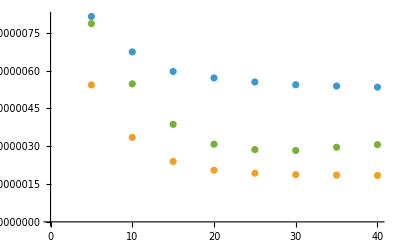

```mathematica
ListPlot[{
{#impactGridCount,#["norm_emit_x"]}&/@raw,
{#impactGridCount,#["norm_emit_x_90"]}&/@raw,
{#impactGridCount,#["emitSI90_x"]}&/@raw
}
]
```

## Solenoid

```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2025-03-20-17-35-58.json"];
raw=Association[#]&/@raw;

raw[[1]]
```

<|L0APhaseOffset→0.,solSet→-0.37,impactGridCount→25.,norm_emit_x→7.1145×10^-6,norm_emit_y→7.1172×10^-6,norm_emit_x_90→2.993×10^-6,norm_emit_y_90→2.9963×10^-6,emitSI90_x→5.1049×10^-6,emitSI90_y→5.2766×10^-6|>

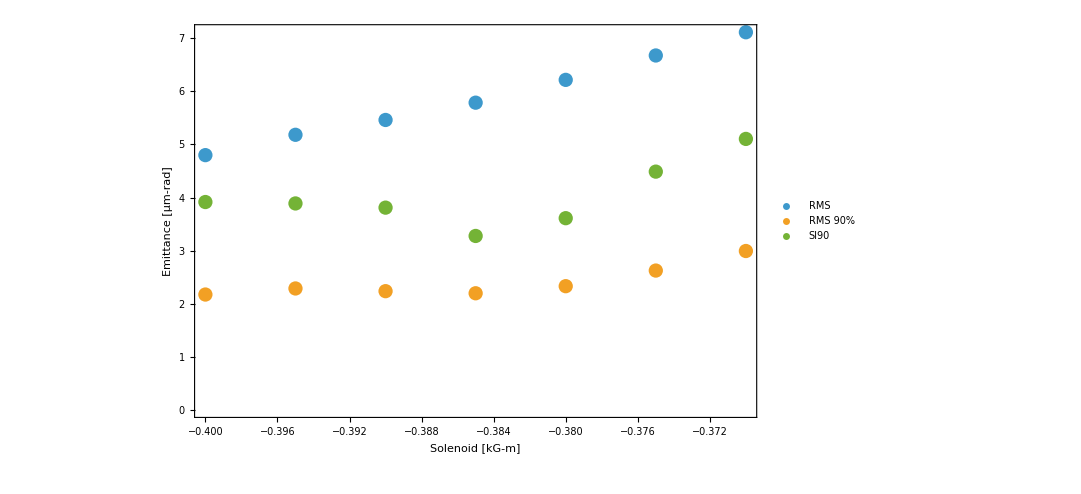

```mathematica
ListPlot[{
{#solSet,10^6#["norm_emit_x"]}&/@raw,
{#solSet,10^6#["norm_emit_x_90"]}&/@raw,
{#solSet,10^6#["emitSI90_x"]}&/@raw
},
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"Solenoid [kG-m]","Emittance [μm-rad]"},
PlotLegends->Placed[{"RMS","RMS 90%","SI90"},{0.9,0.85}]
]
```

## With phase scan

```mathematica
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2025-03-19-17-59-20.json"];*)
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2025-03-20-22-03-56.json"];

raw=Association[#]&/@raw;
```

```mathematica
raw[[1]]
```

<|L0APhaseOffset→-15.,solSet→-0.37,impactGridCount→25.,norm_emit_x→6.9696×10^-6,norm_emit_y→6.9758×10^-6,norm_emit_x_90→2.9351×10^-6,norm_emit_y_90→2.9431×10^-6,emitSI90_x→4.8111×10^-6,emitSI90_y→4.8305×10^-6|>

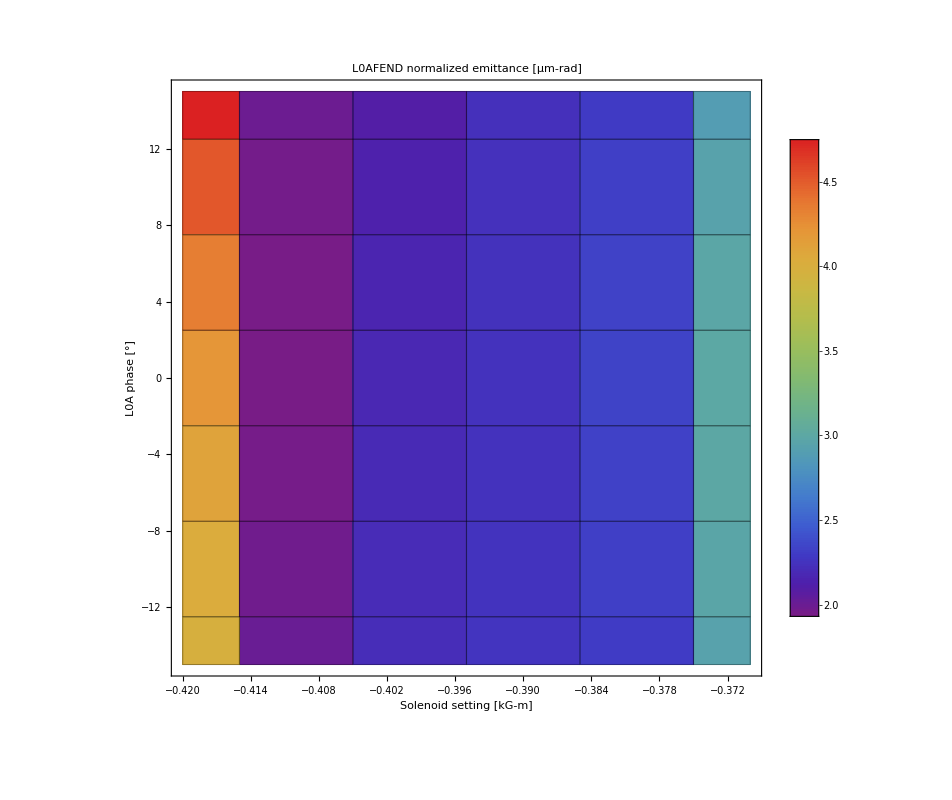

```mathematica
ListDensityPlot[
{#solSet,#L0APhaseOffset,10^6#["norm_emit_x_90"]}&/@raw,
ColorFunction->"Rainbow",
InterpolationOrder->0,
PlotLegends->Automatic,
Mesh->All,
ImageSize->800,
FrameLabel->{"Solenoid setting [kG-m]","L0A phase [°]"},
PlotLabel->"L0AFEND normalized emittance [μm-rad]",
LabelStyle->20
]
```

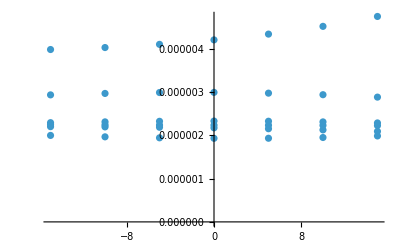

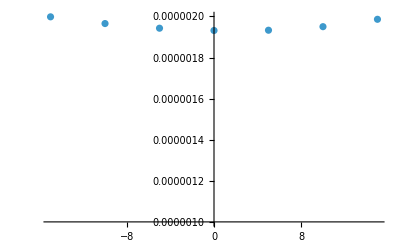

```mathematica
ListPlot[{#L0APhaseOffset,#["norm_emit_x_90"]}&/@raw]
ListPlot[{#L0APhaseOffset,#["norm_emit_x_90"]}&/@raw,PlotRange->{1*^-6,2*^-6}]
```